```mathematica
SetDirectory[NotebookDirectory[]];
data1 = Import["f1Table1_FUNC1_TRAPE.txt","TABLE"];
data2 = Import["f1Table1_FUNC1_S_1_3.txt","TABLE"];
data3 = Import["f1Table1_FUNC1_S_8_3.txt","TABLE"];
data4 = Import["f1Table1_FUNC1_GAUSS.txt","TABLE"];
xcord=1;
ycord=3;
cerror=3;
ctasas=4;

data11=Table[{data1[[i,cerror]],data1[[i,ctasas]]},{i,1,Length[data1],1}];
data12=Table[{data2[[i,cerror]],data2[[i,ctasas]]},{i,1,Length[data2],1}];
data13=Table[{data3[[i,cerror]],data3[[i,ctasas]]},{i,1,Length[data3],1}];
data14=Table[{data4[[i,cerror]],data4[[i,ctasas]]},{i,1,Length[data4],1}];



data1ToPlot = Table[{data1[[i,xcord]],data1[[i,ycord]]},{i,1,Length[data1],1}];
data2ToPlot = Table[{data2[[i,xcord]],data2[[i,ycord]]},{i,1,Length[data2],1}];
data3ToPlot = Table[{data3[[i,xcord]],data3[[i,ycord]]},{i,1,Length[data3],1}];
data4ToPlot = Table[{data4[[i,xcord]],data4[[i,ycord]]},{i,1,Length[data4],1}];
colors = {{Red},{Blue}, {Green}, {Black}};
colors1 = {{Red,Dashed},{Blue,Dashed}, {Green,Dashed}, {Brown,Dashed}};
namestoplot={Style["M. Trapecios",12],Style["M. Simpson 1/3",12],Style["M. Simpson 3/8",12],Style["M. Gauss Legendre",12]};
format = {PlotStyle->colors,PlotLegends->namestoplot,Frame->True,FrameLabel->{"Log h","Log erro"} ,FrameStyle->Directive[Black, Thickness[0.005],Bold,FontSize->16],FrameTicksStyle->{{FontSize->15,Black},{FontSize->15,Black},{FontSize->15,Black},{FontSize->15,Black}},GridLines->Automatic};
```

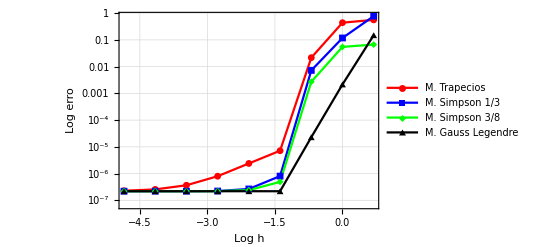

Funcion1.pdf

F1_TRAPECIOS.xlsx

F1_SIMP_1_3.xlsx

F1_SIMP_3_8.xlsx

F1_GAUSS.xlsx

```mathematica
plot1 = ListLogPlot[{data1ToPlot,data2ToPlot, data3ToPlot, data4ToPlot},Joined->True, PlotRange->All,format, PlotMarkers->{Automatic, Small}]
Export["Funcion1.pdf",plot1]
Export["F1_TRAPECIOS.xlsx",data11]
Export["F1_SIMP_1_3.xlsx",data12]
Export["F1_SIMP_3_8.xlsx",data13]
Export["F1_GAUSS.xlsx",data14]
```